# 公式推导

```mathematica
Clear["Global`*"];
q1=θ1[t];
q2=θ2[t];
v=f'[t];
```

```mathematica
T1=m1/2((L1 D[q1, t] Cos[q1]+v)^2+(L1 D[q1, t] Sin[q1])^2)//FullSimplify;
T2=m2/2((L1 D[q1, t] Cos[q1]+L2 D[q2, t] Cos[q2]+v)^2+(L1 D[q1, t] Sin[q1]+L2 D[q2, t] Sin[q2])^2)//FullSimplify;
T=(T1+T2)//FullSimplify;
```

```mathematica
T//TraditionalForm
```

1/2 (m1 (2 L1 f'(t) θ1'(t) cos(θ1(t))+(f'(t))^2+L1^2 (θ1'(t))^2)+m2 ((f'(t)+L1 θ1'(t) cos(θ1(t))+L2 θ2'(t) cos(θ2(t)))^2+(L1 θ1'(t) sin(θ1(t))+L2 θ2'(t) sin(θ2(t)))^2))

```mathematica
V=-m1 g L1 Cos[q1]-m2 g (L1 Cos[q1]+L2 Cos[q2])//FullSimplify;
L=T-V//FullSimplify;
L//TraditionalForm
```

1/2 ((m1+m2) (2 L1 f'(t) θ1'(t) cos(θ1(t))+(f'(t))^2+L1^2 (θ1'(t))^2)+2 L2 m2 θ2'(t) (f'(t) cos(θ2(t))+L1 θ1'(t) cos(θ1(t)-θ2(t)))+L2^2 m2 (θ2'(t))^2)+g L1 (m1+m2) cos(θ1(t))+g L2 m2 cos(θ2(t))

```mathematica
eq1=D[(D[L, (D[q1, t])]), t]-D[L, q1]==0//FullSimplify;
eq2=D[(D[L, (D[q2, t])]), t]-D[L, q2]==0//FullSimplify;
eq1//TraditionalForm
eq2//TraditionalForm
```

L1 ((m1+m2) (f''(t) cos(θ1(t))+g sin(θ1(t))+L1 θ1''(t))+L2 m2 (θ2'(t))^2 sin(θ1(t)-θ2(t))+L2 m2 θ2''(t) cos(θ1(t)-θ2(t)))==0

L2 m2 (f''(t) cos(θ2(t))+g sin(θ2(t))-L1 (θ1'(t))^2 sin(θ1(t)-θ2(t))+L1 θ1''(t) cos(θ1(t)-θ2(t))+L2 θ2''(t))==0

# 一个例子

```mathematica
case={m1->2,m2->1,g->9.8,f'[t]->3t+1,f''[t]->3,L1->0.5,L2->0.3};
equation={eq1,eq2}/.case//FullSimplify;
AppendTo[equation,θ1[0]==10*π/180];
AppendTo[equation,θ2[0]==20*π/180];
AppendTo[equation,θ1'[0]==2];
AppendTo[equation,θ2'[0]==1];
```

```mathematica
res=NDSolve[equation,{θ1,θ2},{t,0,10}];
res
```

{{θ1→InterpolatingFunction[…],θ2→InterpolatingFunction[…]}}

```mathematica
α=θ1/.res[[1]][[1]];
β=θ2/.res[[1]][[2]];
```

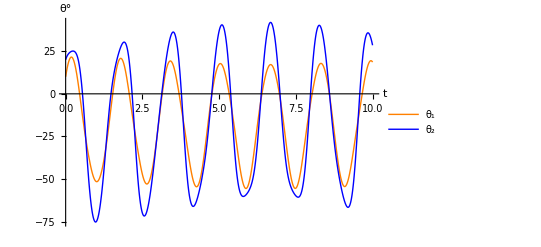

```mathematica
picture=Plot[{180/π α[t],180/π β[t]},{t,0,10},AxesLabel->{"t","θ°"},
LabelStyle->Directive[Medium],
PlotLegends->Placed[{"θ_1","θ_2"},Above],PlotStyle->{Orange,Blue},
PlotTheme->"Classic"
];
picture
```

```mathematica
Export["C:\\Users\\bcynuaa\\Desktop\\angle.png",picture];
Export["C:\\Users\\bcynuaa\\Desktop\\angle.pdf",picture];
```

```mathematica
node0={0,0};
node1={L1 Sin[α[t]],-L1 Cos[α[t]]}/.case;
node2={L1 Sin[α[t]]+L2 Sin[β[t]],-L1 Cos[α[t]]-L2 Cos[β[t]]}/.case;
```

```mathematica
graph=Graphics[{
{Thickness[0.01],Orange,Line[{node0,node1}]},
{Thickness[0.01],Blue,Line[{node1,node2}]},
{Thickness[0.005],Black,Dashed,Line[{node0,-0.1*{3,9.8}}]},
{PointSize[Large],Black,Point[node0]},
{PointSize[Large],Red,Point[node1]},
{PointSize[Large],Red,Point[node2]}
},
Frame->True,
Axes->True,
AxesOrigin->node0,
PlotRange->{{-0.8,0.8},{-1,0}},
AxesLabel->{"x","y"}
];
```

```mathematica
animate=Animate[graph/.t->τ,{τ,0,10},AnimationRunning->False];
animate
```

```mathematica
Export["C:\\Users\\bcynuaa\\Desktop\\animate.gif",animate];
```

```mathematica
graphlist={};
For[i=0,i<10,i++,AppendTo[graphlist,graph/.t->(0.2i)]];
```

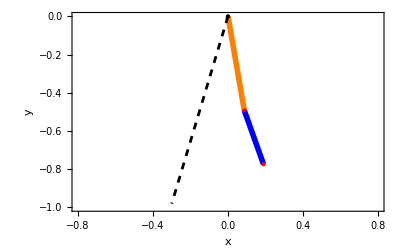
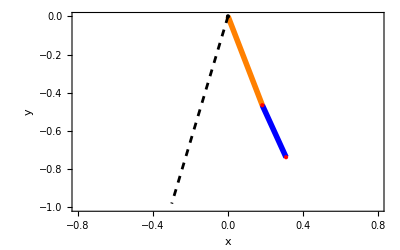
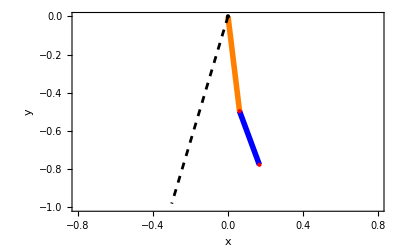
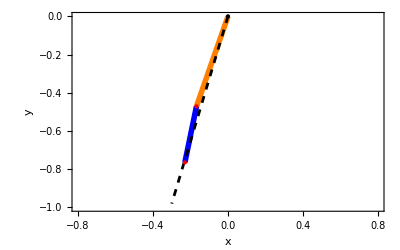
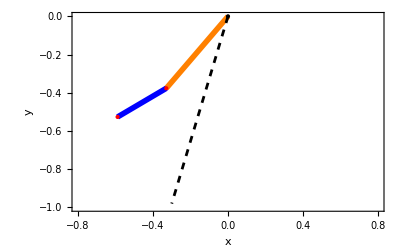
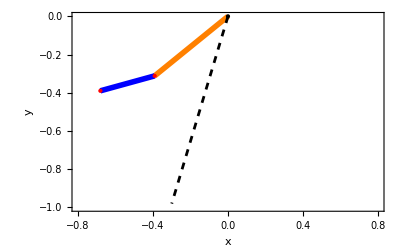
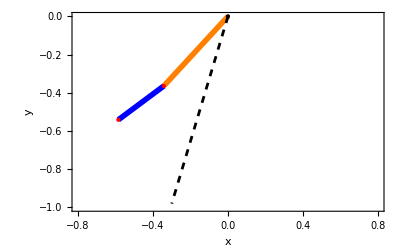
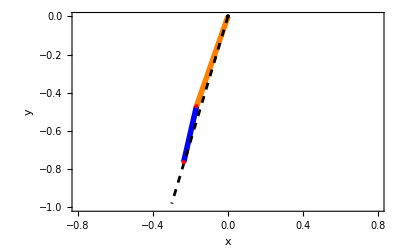

```mathematica
graphlist
```

```mathematica
For[i=0,i<10,i++,Export[StringJoin["C:\\Users\\bcynuaa\\Desktop\\",ToString[i],".png"],graphlist[[i+1]]]];
For[i=0,i<10,i++,Export[StringJoin["C:\\Users\\bcynuaa\\Desktop\\",ToString[i],".pdf"],graphlist[[i+1]]]];
```